{Times_s,Areas_umsq}

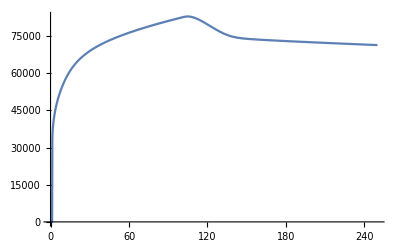

```mathematica
pathBase="/Users/csfloyd/Dropbox/Projects/TCB2Network/ModelDataForPaper/area_100s_pulse/";
test = Import[pathBase <> "r0_100.csv", "Data"];
Print[test[[1]]] (* The first row gives the name of the columns *)
ListPlot[test[[2;;]],Joined->True] (* The second through last row has the actual data*)
```